```mathematica
f0[x_]:=If[0<=x<0.1,1.,0.0];
f1[x_]:=If[0<=x<2,0.5,0.0];
f2[x_]:=If[0<=x<2,x/4,If[2<=x<4,1-x/4,0]];
(*f3[x_]:=Integrate[f1[x-x2]*f2[x2],{x2,0,2*2}];*)
(*f44[x_]:=Integrate[f2[x-x3]*f2[x3],{x3,0,2*2}];*)
(*f5[x_]:=Integrate[f1[x-x4]*f4[x4],{x4,0,4*2}];*)

f3[x_]:=
If[0<=x<2,x^2/16,
If[2<=x<4,(4-(x-2)^2)/16+1/2(x-x^2/8-(2-2^2/8)),
If[4<=x<6,1/2((4-4^2/8)-(x-2-(x-2)^2/8)),0]]];

f4[x_]:=If[0<=x<2,x^3/96,
If[2<=x<4,1/3-x/2+x^2/4-x^3/32,
If[4<=x<6,-11/3+(5 x)/2-x^2/2+x^3/32,
If[6<=x<8,16/3-2 x+x^2/4-x^3/96,0]]]];
(*f5[x_]:=Integrate[f2[x-x5]*f3[x5],{x5,0,10}];
f6[x_]:=Integrate[f3[x-x6]*f3[x6],{x6,0,12}];
f7[x_]:=Integrate[f3[x-x7]*f4[x7],{x7,0,14}];
f8[x_]:=Integrate[f4[x-x8]*f4[x8],{x8,0,16}];*)
f5[x_]:=Piecewise[{{1/768 (-10+x)^4, 8≤x<10}, {x^4/768, 0<x<2}, {1/768 (-2560+2688 x-744 x^2+80 x^3-3 x^4), x==6}, {1/768 (-32 x+24 x^2-x^4), x==2}, {1/192 (-20+40 x-30 x^2+10 x^3-x^4), 2<x<4}, {1/192 (-2620+1560 x-330 x^2+30 x^3-x^4), 6<x<8}, {1/384 (1240-1200 x+420 x^2-60 x^3+3 x^4), 4<x<6}, {1/768 (-720+192 x+120 x^2-40 x^3+3 x^4), x==4}, {0, True}}];
f6[_]:= Piecewise[{{-(-12+x)^5/7680, 10≤x<12}, {x^5/7680, 0<x<2}, {((-10+x)^3 (30-15 x+x^2))/1920, x==8}, {(192-480 x+480 x^2-240 x^3+60 x^4-5 x^5)/7680, 2<x<4}, {(70176-55440 x+17040 x^2-2520 x^3+180 x^4-5 x^5)/3840, 6<x<8}, {(384-480 x+160 x^2-x^5)/7680, x==2}, {(-2432-1360 x+1360 x^2-320 x^3+30 x^4-x^5)/1280, x==6}, {(144-240 x+60 x^3-15 x^4+x^5)/1920, x==4}, {(-351168+196320 x-42720 x^2+4560 x^3-240 x^4+5 x^5)/7680, 8<x<10}, {(-7584+9360 x-4560 x^2+1080 x^3-120 x^4+5 x^5)/3840, 4<x<6}, {0, True}}] ; 
f7[x_]:= Piecewise[{{(-14+x)^6/92160, 12≤x<14}, {x^6/92160, 0<x<2}, {-(x (-384+480 x-160 x^2+x^5))/92160, x==2}, {(-3584+22080 x-28560 x^2+11840 x^3-2100 x^4+168 x^5-5 x^6)/46080, x==6}, {(-386848+376320 x-150360 x^2+31360 x^3-3570 x^4+210 x^5-5 x^6)/23040, 6<x<8}, {(-6193152+4078080 x-1031040 x^2+132320 x^3-9240 x^4+336 x^5-5 x^6)/92160, x==10}, {(-224+672 x-840 x^2+560 x^3-210 x^4+42 x^5-3 x^6)/46080, 2<x<4}, {(-6686176+3612000 x-800520 x^2+93520 x^3-6090 x^4+210 x^5-3 x^6)/46080, 10<x<12}, {(369600-576960 x+254400 x^2-50240 x^3+5040 x^4-252 x^5+5 x^6)/46080, x==8}, {(28224-18240 x+3600 x^2-800 x^3+420 x^4-84 x^5+5 x^6)/92160, x==4}, {(7627648-5376000 x+1548960 x^2-232960 x^3+19320 x^4-840 x^5+15 x^6)/92160, 8<x<10}, {(85568-127680 x+78960 x^2-25760 x^3+4620 x^4-420 x^5+15 x^6)/92160, 4<x<6}, {0, True}}];
f8[x_]:=  Piecewise[{{-(-16+x)^7/1290240, 14≤x<16}, {x^7/1290240, 0<x<2}, {((-14+x)^4 (-4032+1288 x-112 x^2+3 x^3))/645120, x==12}, {(15218688-17489920 x+8547840 x^2-2293760 x^3+362880 x^4-33600 x^5+1680 x^6-35 x^7)/1290240, 6<x<8}, {(428418048-281039360 x+77978880 x^2-11858560 x^3+1068480 x^4-57120 x^5+1680 x^6-21 x^7)/1290240, 10<x<12}, {(4534272-2885120 x+913920 x^2-253120 x^3+58240 x^4-8064 x^5+560 x^6-15 x^7)/1290240, x==6}, {(97870848-88874240 x+31261440 x^2-5679520 x^3+586880 x^4-34944 x^5+1120 x^6-15 x^7)/1290240, x==10}, {(1024-3584 x+5376 x^2-4480 x^3+2240 x^4-672 x^5+112 x^6-7 x^7)/1290240, 2<x<4}, {(-5120+8960 x-5376 x^2+1120 x^3-x^7)/1290240, x==2}, {(-116736+117376 x-43008 x^2+7280 x^3-1120 x^4+336 x^5-56 x^6+3 x^7)/645120, x==4}, {(-4236800+4081280 x-1935360 x^2+510160 x^3-76160 x^4+6384 x^5-280 x^6+5 x^7)/322560, x==8}, {(-574872576+304213504 x-68334336 x^2+8462720 x^3-624960 x^4+27552 x^5-672 x^6+7 x^7)/1290240, 12<x<14}, {(-457728+799232 x-596736 x^2+246400 x^3-60480 x^4+8736 x^5-672 x^6+21 x^7)/1290240, 4<x<6}, {(-131581952+110960640 x-39621120 x^2+7741440 x^3-891520 x^4+60480 x^5-2240 x^6+35 x^7)/1290240, 8<x<10}, {0, True}}];
f9[x_]:=Piecewise[{{4.84406001984127*^-8 (-18.+x)^8, 16.≤x<18.}, {4.84406001984127*^-8 x^8, 0.<x≤2.}, {4.84406001984127*^-8 (-9.3388032*^7+1.21749504*^8 x-6.995968*^7 x^2+2.279424*^7 x^3-4.58752*^6 x^4+580608. x^5-44800. x^6+1920. x^7-35. x^8), x==8.}, {4.84406001984127*^-8 (-4.52697984*^9+3.427344384*^9 x-1.12415744*^9 x^2+2.0794368*^8 x^3-2.371712*^7 x^4+1.709568*^6 x^5-76160. x^6+1920. x^7-21. x^8), x==12.}, {4.84406001984127*^-8 (-2304.+8192. x-14336. x^2+14336. x^3-8960. x^4+3584. x^5-896. x^6+128. x^7-7. x^8), x==4.}, {3.875248015873016*^-7 (-1.7341344*^7+2.2925952*^7 x-1.3202784*^7 x^2+4.316256*^6 x^3-873180. x^4+111384. x^5-8694. x^6+378. x^7-7. x^8), 6.<x<8.}, {3.875248015873016*^-7 (-1.328100192*^9+1.0186848*^9 x-3.3859728*^8 x^2+6.361488*^7 x^3-7.38234*^6 x^4+541800. x^5-24570. x^6+630. x^7-7. x^8), 10.<x<12.}, {3.875248015873016*^-7 (-288.+1152. x-2016. x^2+2016. x^3-1260. x^4+504. x^5-126. x^6+18. x^7-1. x^8), 2.<x<4.}, {3.875248015873016*^-7 (-3.454343136*^9+1.803699072*^9 x-4.0943952*^8 x^2+5.2833312*^7 x^3-4.24242*^6 x^4+217224. x^5-6930. x^6+126. x^7-1. x^8), 14.<x<16.}, {4.84406001984127*^-8 (7.51140864*^9-4.598980608*^9 x+1.216854016*^9 x^2-1.82224896*^8 x^3+1.692544*^7 x^4-999936. x^5+36736. x^6-768. x^7+7. x^8), x==14.}, {1.937624007936508*^-7 (6.373415232*^9-3.982374144*^9 x+1.078564032*^9 x^2-1.65396672*^8 x^3+1.571724*^7 x^4-948528. x^5+35532. x^6-756. x^7+7. x^8), 12.<x<14.}, {1.937624007936508*^-7 (589248.-1.177344*^6 x+1.02816*^6 x^2-512064. x^3+158760. x^4-31248. x^5+3780. x^6-252. x^7+7. x^8), 4.<x<6.}, {4.84406001984127*^-8 (1.769472*^6-3.661824*^6 x+3.196928*^6 x^2-1.591296*^6 x^3+492800. x^4-96768. x^5+11648. x^6-768. x^7+21. x^8), x==6.}, {4.84406001984127*^-8 (1.077018624*^9-1.052655616*^9 x+4.4384256*^8 x^2-1.0565632*^8 x^3+1.548288*^7 x^4-1.426432*^6 x^5+80640. x^6-2560. x^7+35. x^8), x==10.}, {9.68812003968254*^-8 (9.87599232*^8-9.652608*^8 x+4.0961088*^8 x^2-9.834048*^7 x^3+1.457064*^7 x^4-1.3608*^6 x^5+78120. x^6-2520. x^7+35. x^8), 8.<x<10.}, {0., True}}]
g9[x_]:=Piecewise[{{4.84406001984127*^-8 (-18.+x)^8, 16.≤x<18.}, {4.84406001984127*^-8 x^8, 0.<x≤2.}, {4.84406001984127*^-8 (-9.3388032*^7+1.21749504*^8 x-6.995968*^7 x^2+2.279424*^7 x^3-4.58752*^6 x^4+580608. x^5-44800. x^6+1920. x^7-35. x^8), x==8.}, {4.84406001984127*^-8 (-4.52697984*^9+3.427344384*^9 x-1.12415744*^9 x^2+2.0794368*^8 x^3-2.371712*^7 x^4+1.709568*^6 x^5-76160. x^6+1920. x^7-21. x^8), x==12.}, {4.84406001984127*^-8 (-2304.+8192. x-14336. x^2+14336. x^3-8960. x^4+3584. x^5-896. x^6+128. x^7-7. x^8), x==4.}, {3.875248015873016*^-7 (-1.7341344*^7+2.2925952*^7 x-1.3202784*^7 x^2+4.316256*^6 x^3-873180. x^4+111384. x^5-8694. x^6+378. x^7-7. x^8), 6.<x<8.}, {3.875248015873016*^-7 (-1.328100192*^9+1.0186848*^9 x-3.3859728*^8 x^2+6.361488*^7 x^3-7.38234*^6 x^4+541800. x^5-24570. x^6+630. x^7-7. x^8), 10.<x<12.}, {3.875248015873016*^-7 (-288.+1152. x-2016. x^2+2016. x^3-1260. x^4+504. x^5-126. x^6+18. x^7-1. x^8), 2.<x<4.}, {3.875248015873016*^-7 (-3.454343136*^9+1.803699072*^9 x-4.0943952*^8 x^2+5.2833312*^7 x^3-4.24242*^6 x^4+217224. x^5-6930. x^6+126. x^7-1. x^8), 14.<x<16.}, {4.84406001984127*^-8 (7.51140864*^9-4.598980608*^9 x+1.216854016*^9 x^2-1.82224896*^8 x^3+1.692544*^7 x^4-999936. x^5+36736. x^6-768. x^7+7. x^8), x==14.}, {1.937624007936508*^-7 (6.373415232*^9-3.982374144*^9 x+1.078564032*^9 x^2-1.65396672*^8 x^3+1.571724*^7 x^4-948528. x^5+35532. x^6-756. x^7+7. x^8), 12.<x<14.}, {1.937624007936508*^-7 (589248.-1.177344*^6 x+1.02816*^6 x^2-512064. x^3+158760. x^4-31248. x^5+3780. x^6-252. x^7+7. x^8), 4.<x<6.}, {4.84406001984127*^-8 (1.769472*^6-3.661824*^6 x+3.196928*^6 x^2-1.591296*^6 x^3+492800. x^4-96768. x^5+11648. x^6-768. x^7+21. x^8), x==6.}, {4.84406001984127*^-8 (1.077018624*^9-1.052655616*^9 x+4.4384256*^8 x^2-1.0565632*^8 x^3+1.548288*^7 x^4-1.426432*^6 x^5+80640. x^6-2560. x^7+35. x^8), x==10.}, {9.68812003968254*^-8 (9.87599232*^8-9.652608*^8 x+4.0961088*^8 x^2-9.834048*^7 x^3+1.457064*^7 x^4-1.3608*^6 x^5+78120. x^6-2520. x^7+35. x^8), 8.<x<10.}, {0., True}}]
f10[x_]:=Piecewise[{{-2.6911444554673723*^-9 (-20.+x)^9, 18.≤x<20.}, {2.6911444554673723*^-9 x^9, 0.<x≤2.}, {5.382288910934745*^-9 (1.1250590464*^11-9.8439264*^10 x+3.80241792*^10 x^2-8.4993216*^9 x^3+1.20998304*^9 x^4-1.13652*^8 x^5+7.0392*^6 x^6-277200. x^7+6300. x^8-63. x^9), 10.<x<12.}, {5.382288910934745*^-9 (4.14678528*^8-6.24288384*^8 x+4.12667136*^8 x^2-1.58433408*^8 x^3+3.8846304*^7 x^4-6.286896*^6 x^5+668304. x^6-44712. x^7+1701. x^8-28. x^9), x==8.}, {5.382288910934745*^-9 (5.489638912*^10-4.7811606912*^10 x+1.83363264*^10 x^2-4.06316736*^9 x^3+5.7253392*^8 x^4-5.3152848*^7 x^5+3.2508*^6 x^6-126360. x^7+2835. x^8-28. x^9), x==12.}, {1.076457782186949*^-8 (2.9938304*^8-4.4686656*^8 x+2.9570688*^8 x^2-1.1371584*^8 x^3+2.795184*^7 x^4-4.54104*^6 x^5+485520. x^6-32760. x^7+1260. x^8-21. x^9), 6.<x<8.}, {2.6911444554673723*^-9 (5120.-23040. x+46080. x^2-53760. x^3+40320. x^4-20160. x^5+6720. x^6-1440. x^7+180. x^8-9. x^9), 2.<x<4.}, {1.076457782186949*^-8 (4.0519588736*^11-2.4451632576*^11 x+6.51365568*^10 x^2-1.005590208*^10 x^3+9.9194256*^8 x^4-6.486984*^7 x^5+2.814*^6 x^6-78120. x^7+1260. x^8-9. x^9), 14.<x<16.}, {5.382288910934745*^-9 (2048.-10368. x+20736. x^2-24192. x^3+18144. x^4-9072. x^5+3024. x^6-648. x^7+81. x^8-4. x^9), x==4.}, {5.382288910934745*^-9 (2.10058128896*^11-1.24356352896*^11 x+3.2466583296*^10 x^2-4.91327424*^9 x^3+4.75499808*^8 x^4-3.0545424*^7 x^5+1.303344*^6 x^6-35640. x^7+567. x^8-4. x^9), x==16.}, {2.6911444554673723*^-9 (-1.47159290368*^12+7.6139645184*^11 x-1.7431921152*^11 x^2+2.319426816*^10 x^3-1.97765568*^9 x^4+1.1210976*^8 x^5-4.22688*^6 x^6+102240. x^7-1440. x^8+9. x^9), 16.<x<18.}, {1.076457782186949*^-8 (-2.94784*^6+6.62976*^6 x-6.624*^6 x^2+3.85728*^6 x^3-1.44144*^6 x^4+357840. x^5-58800. x^6+6120. x^7-360. x^8+9. x^9), 4.<x<6.}, {5.382288910934745*^-9 (-1.61836973568*^11+1.14721474176*^11 x-3.5841367296*^10 x^2+6.471384192*^9 x^3-7.44285024*^8 x^4+5.6582064*^7 x^5-2.845584*^6 x^6+91368. x^7-1701. x^8+14. x^9), x==14.}, {5.382288910934745*^-9 (-4.845056*^6+1.0606464*^7 x-1.0596096*^7 x^2+6.16896*^6 x^3-2.304288*^6 x^4+571536. x^5-93744. x^6+9720. x^7-567. x^8+14. x^9), x==6.}, {1.076457782186949*^-8 (-2.1463551616*^11+1.5394671936*^11 x-4.871002752*^10 x^2+8.91852864*^9 x^3-1.04103216*^9 x^4+8.034264*^7 x^5-4.10088*^6 x^6+133560. x^7-2520. x^8+21. x^9), 12.<x<14.}, {5.382288910934745*^-9 (-8.06362624*^9+8.888393088*^9 x-4.3436736*^9 x^2+1.22883264*^9 x^3-2.2126608*^8 x^4+2.6227152*^7 x^5-2.0412*^6 x^6+100440. x^7-2835. x^8+35. x^9), x==10.}, {5.382288910934745*^-9 (-1.349409536*^10+1.4960736*^10 x-7.3358208*^9 x^2+2.0846784*^9 x^3-3.7761696*^8 x^4+4.5108*^7 x^5-3.5448*^6 x^6+176400. x^7-5040. x^8+63. x^9), 8.<x<10.}, {0., True}}]
PoisD[μ_,n_]:=(ⅇ^-μ μ^n)/(n!);
PoisDx[μ_,x_]:=(ⅇ^-μ μ^x)/Gamma[x+1];
F[i_][x_]:=ToExpression["f"<>ToString[i]][x];
sumP[μ_,x_,m_]:=∑_(i=0)^m PoisD[μ,i]F[i][x];
```

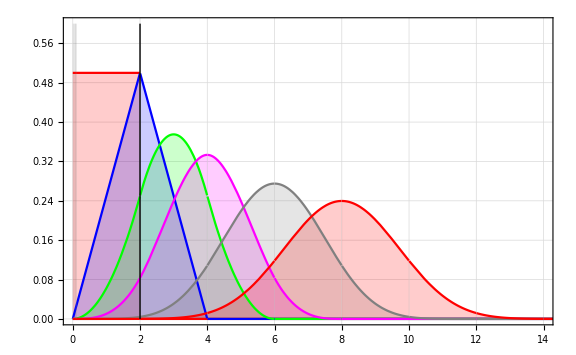

```mathematica
lineStyle={Thick,Black};
line1=Line[{{2.,0},{2.,0.6}}];

Plot[{f0[x],f1[x],f2[x],f3[x],f4[x],f6[x],f8[x]},{x,0,16},
PlotRange->{{0,14},{0,0.6}},
Frame->True,
Filling->Axis,
PlotStyle->{Gray,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
Epilog->{Directive[lineStyle],line1}
]
```

k =4.

Integral sumP = 0.962152

NIntegrate[x*sumP[k,x]=3.79556

Sqrt[NIntegrate[x^2*sumP[k,x] =4.39202

Integral PoisD[k,x] = 0.993828

NIntegrate[x*PoisDx[k,x] =4.00131

Sqrt[NIntegrate[x^2*PoisDx[k,x]] =4.47202

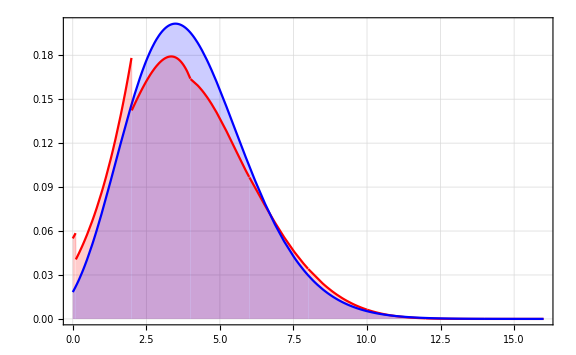

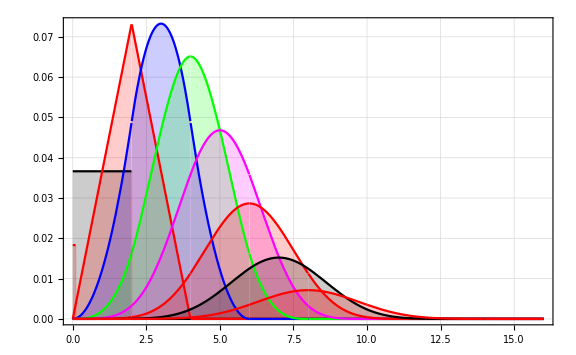

1

4/ⅇ^4

8/ⅇ^4

```mathematica
k=4.0;
sumP[μ_,x_]:=PoisD[μ,0] f0[x]+PoisD[μ,1] f1[x]+PoisD[μ,2] f2[x]+PoisD[μ,3] f3[x]+PoisD[μ,4] f4[x]+PoisD[μ,5] f5[x]+PoisD[μ,6] f6[x]+PoisD[μ,7] f7[x]+PoisD[μ,8] f8[x];
Print["k =",k]
Print["Integral sumP = ",Integrate[sumP[k,x],{x,0,16}]]
Print["NIntegrate[x*sumP[k,x]=", NIntegrate[x*sumP[k,x],{x,0,16}]]
Print["Sqrt[NIntegrate[x^2*sumP[k,x] =",Sqrt[NIntegrate[x^2*sumP[k,x],{x,0,16}]]]
Print["Integral PoisD[k,x] = ",NIntegrate[PoisDx[k,x],{x,0,16}]]
Print["NIntegrate[x*PoisDx[k,x] =",NIntegrate[x*PoisDx[k,x],{x,0,16}]]
Print["Sqrt[NIntegrate[x^2*PoisDx[k,x]] =",Sqrt[NIntegrate[x^2*PoisDx[k,x],{x,0,16}]]]
μ=4.0; n=8;
Plot[{sumP[μ,x],PoisDx[4,x]},{x,0,16},
PlotRange->{{0,16},{0,All}},
Frame->True,
Filling->Axis,
PlotStyle->{Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]
Plot[{PoisD[k,0] f0[x],PoisD[k,1] f1[x],PoisD[k,2] f2[x],PoisD[k,3] f3[x],PoisD[k,4] f4[x],PoisD[k,5] f5[x],PoisD[k,6] f6[x],PoisD[k,7] f7[x],PoisD[k,8] f8[x]},{x,0,16},
PlotRange->{{0,16},{0,All}},
Frame->True,
Filling->Axis,
PlotStyle->{Red,Black,Red,Blue,Green,Magenta},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic
]

Integrate[f8[x],{x,0,16}]
PoisD[4,1]
PoisD[4,2]
```

```mathematica
PoisD[μ,0] f0[0]*Exp[-μ]/10.
PoisD[μ,0] f0[0]/10
PoisD[μ,0]
```

0.000335463

0.0183156

0.0183156